```mathematica
im2real[x_]:={Re@x,Im@x};
real2im@{x_,y_}:=x+y*I;
```

```mathematica
(*f[x_] is the parametrization of the rectangle]*)
f[x_]=Piecewise[{{Sqrt[2]/2+(x-Sqrt[2]/2)*I,0<=x<=Sqrt[2]},{(3Sqrt[2]/2-x)+Sqrt[2]/2*I,Sqrt[2]<x<=2*Sqrt[2]},{-Sqrt[2]/2+(5Sqrt[2]/2-x)*I,2*Sqrt[2]<x<=3*Sqrt[2]},{x-7Sqrt[2]/2+(-Sqrt[2]/2)*I,3*Sqrt[2]<x<=4*Sqrt[2]}},Infinity];
points=Table[f@x,{x,0,4*Sqrt[2],0.01}];
```

```mathematica
Min@Table[Norm@x,{x,points}]
a0=First@MinimalBy[points,Norm]
```

0.707107

0.000252532-0.707107 ⅈ

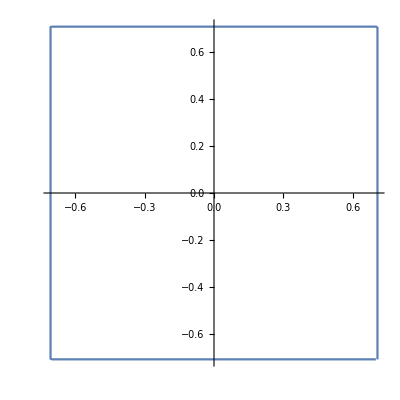

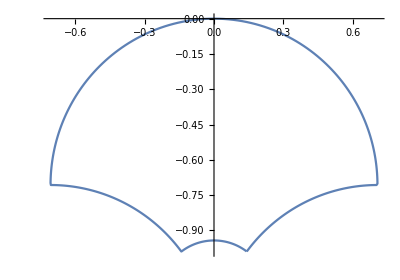

```mathematica
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
(*g[x_]=(x+Sqrt[2]/2)/(1+x Sqrt[2]/2);*)
g[x_]:=(x+a0)/(1+x*Conjugate[a0]);
points = g/@points;
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
```

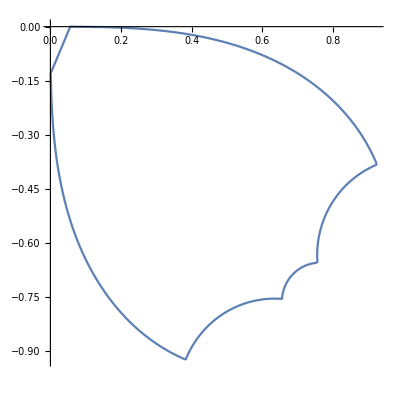

```mathematica
points = Sqrt/@points;
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
(*b0 = Sqrt[Sqrt[2]/2];*)
b0=g[0];
h[x_] := (x-b0)/(1-Conjugate[b0]*x);
points = h/@points;
(*points//.{x_List}:>x*)
points//.{x_List}:>x;
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True];
```

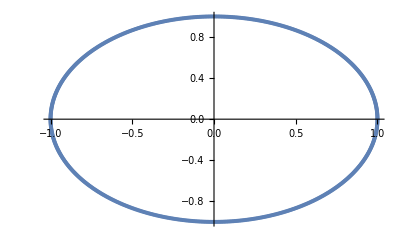

```mathematica
disk=Table[Cos[x/100]+I*Sin[x/100],{x,0,628}];
ListPlot[ReIm@disk]
```

```mathematica
points=Table[f@x,{x,0,4*Sqrt[2],0.01}];
```

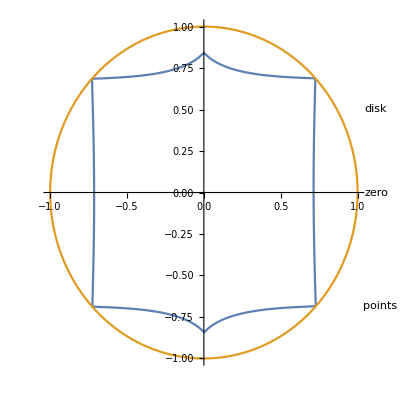

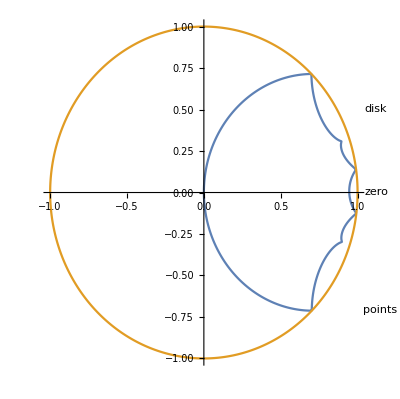

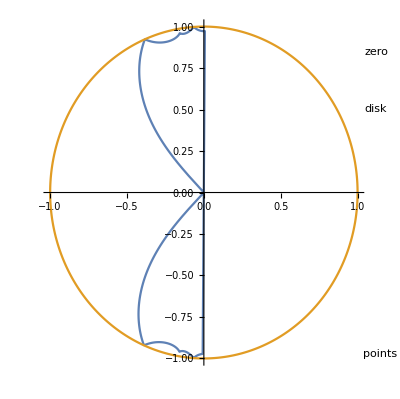

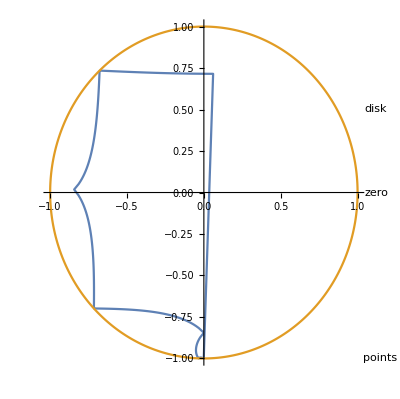

```mathematica
center=0;
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"],Labeled[{ReIm@center},"zero"]},AspectRatio->Automatic,Joined->True]
a0=First@MinimalBy[points,Norm];
g[x_]:=(x-a0)/(1-x*Conjugate[a0]);
points=g/@points;
center=g@center;
"S";
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"],Labeled[{ReIm@center},"zero"]},AspectRatio->Automatic,Joined->True]
points=points*Sign@a0;
center=center*Sign@a0;
"Spin";
(*ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"]},AspectRatio->Automatic]*)
points=Sqrt/@points;
center=Sqrt@center;
"Sqrt";
(*ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"]},AspectRatio->Automatic]*)
points=points/Sign@a0;
center=center/Sign@a0;
"Spin";
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"],Labeled[{ReIm@center},"zero"]},AspectRatio->Automatic,Joined->True]
b0=Sqrt@(g[0]*Sign@a0)/Sign@a0;
h[x_] := (x-b0)/(1-Conjugate[b0]*x);
points=h/@points;
center=h@center;
"S";
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"],Labeled[{ReIm@center},"zero"]},AspectRatio->Automatic,Joined->True]
```